```mathematica
Clear[Evaluate[Context[]<>"*"]]
```

```mathematica
c=137.036;
m=1;
q=-1;
χ=q/m/c;
ω=10;
k=ω/c;
f0=550;
on=2;
const=2;
off=2;

Ex[t]:=-f0/Sqrt[2]*Sin[ω*t-k*z[t]];

Ey[t]:=f0/Sqrt[2]*Cos[ω*t-k*z[t]];
Ext[t]:=-f0*ω/Sqrt[2]*Cos[ω*t-k*z[t]];
Eyt[t]:=f0*ω/Sqrt[2]*-Sin[ω*t-k*z[t]];
Exz[t]:=f0*k/Sqrt[2]*Cos[ω*t-k*z[t]];
Eyz[t]:=-f0*k/Sqrt[2]*-Sin[ω*t-k*z[t]];

s=NDSolve[{(vx'[t]/Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]+vx[t]*(1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2)^(-3/2)*(vx[t]*vx'[t]+vy[t]*vy'[t]+vz[t]*vz'[t])/c^2)==(q*(-f0/Sqrt[2]*Sin[ω*t-k*z[t]])+q/c*(-vz[t]*(-f0/Sqrt[2]*Sin[ω*t-k*z[t]]))+1/Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*χ/c^2*vx[t]*(ζx'[t]*(-f0/Sqrt[2]*Cos[ω*t-k*z[t]])+ζy'[t]*(-f0/Sqrt[2]*Sin[ω*t-k*z[t]])+τx'[t]*(-f0/Sqrt[2]*Sin[ω*t-k*z[t]])+τy'[t]*(f0/Sqrt[2]*Cos[ω*t-k*z[t]]))+1/Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*χ/c^2*vx[t]*(ζx[t]*(-(f0*ω/Sqrt[2]*-Sin[ω*t-k*z[t]]))+ζy[t]*(-f0*ω/Sqrt[2]*Cos[ω*t-k*z[t]])+τx[t]*(-f0*ω/Sqrt[2]*Cos[ω*t-k*z[t]])+τy[t]*(f0*ω/Sqrt[2]*-Sin[ω*t-k*z[t]]))+1/Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*χ/c^2*vx[t]*(vz[t]*ζx[t]*(-(-f0*k/Sqrt[2]*-Sin[ω*t-k*z[t]]))+vz[t]*ζy[t]*(f0*k/Sqrt[2]*Cos[ω*t-k*z[t]])+vz[t]*τx[t]*(f0*k/Sqrt[2]*Cos[ω*t-k*z[t]])+vz[t]*τy[t]*(-f0*k/Sqrt[2]*-Sin[ω*t-k*z[t]]))-χ/c*Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*(-ζz'[t]*(f0/Sqrt[2]*Cos[ω*t-k*z[t]]))-χ/c*Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*(-ζz[t]*(f0*ω/Sqrt[2]*-Sin[ω*t-k*z[t]]))-χ/c*Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*(-vz[t]*ζz[t]*(-f0*k/Sqrt[2]*-Sin[ω*t-k*z[t]]))+χ*q/c^3/m*(1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2)*(vx[t]*(-f0/Sqrt[2]*Sin[ω*t-k*z[t]])+vy[t]*(f0/Sqrt[2]*Cos[ω*t-k*z[t]]))*(-ζz[t]*(f0/Sqrt[2]*Cos[ω*t-k*z[t]])))/(m-χ/c^2*(ζx[t]*(-f0/Sqrt[2]*Cos[ω*t-k*z[t]])+ζy[t]*(-f0*ω/Sqrt[2]*Cos[ω*t-k*z[t]])+τx[t]*(-f0*ω/Sqrt[2]*Cos[ω*t-k*z[t]])+τy[t]*(f0/Sqrt[2]*Cos[ω*t-k*z[t]]))),(vy'[t]/Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]+vy[t]*(1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2)^(-3/2)*(vx[t]*vx'[t]+vy[t]*vy'[t]+vz[t]*vz'[t])/c^2)==(q*(f0/Sqrt[2]*Cos[ω*t-k*z[t]])+q/c*(-vz[t]*(f0/Sqrt[2]*Cos[ω*t-k*z[t]]))+1/Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*χ/c^2*vy[t]*(ζx'[t]*(-Ey[t])+ζy'[t]*Ex[t]+τx'[t]*Ex[t]+τy'[t]*Ey[t])+1/Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*χ/c^2*vy[t]*(ζx[t]*(-Eyt[t])+ζy[t]*Ext[t]+τx[t]*Ext[t]+τy[t]*Eyt[t])+1/Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*χ/c^2*vy[t]*(vz[t]*ζx[t]*(-Eyz[t])+vz[t]*ζy[t]*Exz[t]+vz[t]*τx[t]*Exz[t]+vz[t]*τy[t]*Eyz[t])-χ/c*Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*(ζz'[t]*Ex[t])-χ/c*Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*(ζz[t]*Ext[t])-χ/c*Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*(vz[t]*ζz[t]*Exz[t])+χ*q/c^3/m*(1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2)*(vx[t]*Ex[t]+vy[t]*Ey[t])*(ζz[t]*Ex[t]))/(m-χ/c^2*(ζx[t]*(-Ey[t])+ζy[t]*(Ex[t])+τx[t]*Ex[t]+τy[t]*Ey[t])),(vz'[t]/Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]+vz[t]*(1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2)^(-3/2)*(vx[t]*vx'[t]+vy[t]*vy'[t]+vz[t]*vz'[t])/c^2)==(q/c*(vx[t]*Ex[t]+vy[t]*Ey[t])+χ*Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*(ζx[t]*(-Eyz[t])+ζy[t]*Exz[t]+τx[t]*Exz[t]+τy[t]*Eyz[t])+1/Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*χ/c^2*vz[t]*(ζx'[t]*(-Ey[t])+ζy'[t]*Ex[t]+τx'[t]*Ex[t]+τy'[t]*Ey[t])+1/Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*χ/c^2*vz[t]*(ζx[t]*(-Eyt[t])+ζy[t]*Ext[t]+τx[t]*Ext[t]+τy[t]*Eyt[t])+1/Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*χ/c^2*vz[t]*(vz[t]*ζx[t]*(-Eyz[t])+vz[t]*ζy[t]*Exz[t]+vz[t]*τx[t]*Exz[t]+vz[t]*τy[t]*Eyz[t])-χ/c*Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*(ζx'[t]*Ey[t]-ζy'[t]*Ex[t])-χ/c*Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*(ζx[t]*Eyt[t]-ζy[t]*Ext[t])-χ/c*Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*(vz[t]*ζx[t]*Eyz[t]-vz[t]*ζy[t]*Exz[t])+χ*q/c^3/m*(1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2)*(vx[t]*Ex[t]+vy[t]*Ey[t])*(ζx[t]*Ey[t]-ζy[t]*Ex[t]))/(m-χ/c^2*(ζx[t]*(-Ey[t])+ζy[t]*(Ex[t])+τx[t]*Ex[t]+τy[t]*Ey[t])),ζx'[t]==χ*Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*(-ζz[t]*Ex[t]-τz[t]*Ey[t]),ζy'[t]==χ*Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*(-ζz[t]*Ey[t]+τz[t]*Ex[t]),ζz'[t]==χ*Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*(ζx[t]*Ex[t]+ζy[t]*Ey[t]+τx[t]*Ey[t]-τy[t]*Ex[t]),τx'[t]==χ*Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*(ζz[t]*Ey[t]-τz[t]*Ex[t]),τy'[t]==χ*Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*(-ζz[t]*Ex[t]-τz[t]*Ey[t]),τz'[t]==χ*Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2]*(ζy[t]*Ex[t]-ζx[t]*Ey[t]+τx[t]*Ex[t]+τy[t]*Ey[t]),x'[t]==vx[t],y'[t]==vy[t],z'[t]==vz[t],vx[0]==0,vy[0]==0,vz[0]==0,ζx[0]==0,ζy[0]==0,ζz[0]==1/2,τx[0]==0,τy[0]==0,τz[0]==0,x[0]==0,y[0]==0,z[0]==0},{vx,vy,vz,ζx,ζy,ζz,τx,τy,τz,x,y,z},{t,0,3}];
```

NDSolve::ntdv: 无法求得一个明确的导数公式. 考虑使用选项设置 SolveDelayed -> True.

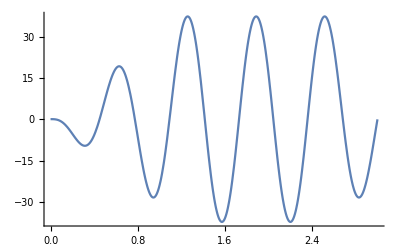

```mathematica
Plot[Evaluate[vx[t]/.s],{t,0,3},PlotRange->All]
```

```mathematica
D[(1-(vx[t]^2+vy[t]^2+vz[t]^2)/cc^2)^(-1/2)*vx[t],t]
```

vx'[t]/(√(1-(vx[t]^2+vy[t]^2+vz[t]^2)/cc^2))+(vx[t] (2 vx[t] vx'[t]+2 vy[t] vy'[t]+2 vz[t] vz'[t]))/(2 cc^2 (1-(vx[t]^2+vy[t]^2+vz[t]^2)/cc^2)^(3/2))

```mathematica
(*Ex[t]:=-f0/Sqrt[2]*Piecewise[{{(ω*t-k*z[t])*Sin[(ω*t-k*z[t])]/2/Pi/on,ω*t-k*z[t]>0 && ω*t-k*z[t] < 2*Pi*on},{Sin[ω*t-k*z[t]],ω*t-k*z[t] < 2*Pi*(on+const)},{(-(ω*t-k*z[t])+2*Pi*(on+const+off))*Sin[ω*t-k*z[t]]/2/Pi/off,ω*t-k*z[t] < 2*Pi*(on+const+off)}}];*)
(*Ext[t]:=-f0*ω/Sqrt[2]*Piecewise[{{(Sin[ω*t-k*z[t]]+(ω*t-k*z[t])*Cos[(ω*t-k*z[t])])/2/Pi/on,ω*t-k*z[t]>0 && ω*t-k*z[t] < 2*Pi*on},{Cos[ω*t-k*z[t]],ω*t-k*z[t] < 2*Pi*(on+const)},{(-Sin[ω*t-k*z[t]]+(-(ω*t-k*z[t])+2*Pi*(on+const+off))*Cos[ω*t-k*z[t]])/2/Pi/off,ω*t-k*z[t] < 2*Pi*(on+const+off)}}];
(*Ey[t]:=f0/Sqrt[2]*Piecewise[{{(ω*t-k*z[t])*Cos[(ω*t-k*z[t])]/2/Pi/on,ω*t-k*z[t]>0 && ω*t-k*z[t] < 2*Pi*on},{Cos[ω*t-k*z[t]],ω*t-k*z[t] < 2*Pi*(on+const)},{(-(ω*t-k*z[t])+2*Pi*(on+const+off))*Cos[ω*t-k*z[t]]/2/Pi/off,ω*t-k*z[t] < 2*Pi*(on+const+off)}}];*)
Eyt[t]:=f0*ω/Sqrt[2]*Piecewise[{{(Cos[ω*t-k*z[t]]-(ω*t-k*z[t])*Sin[(ω*t-k*z[t])])/2/Pi/on,ω*t-k*z[t]>0 && ω*t-k*z[t] < 2*Pi*on},{-Sin[ω*t-k*z[t]],ω*t-k*z[t] < 2*Pi*(on+const)},{(-Cos[ω*t-k*z[t]]-(-(ω*t-k*z[t])+2*Pi*(on+const+off))*Sin[ω*t-k*z[t]])/2/Pi/off,ω*t-k*z[t] < 2*Pi*(on+const+off)}}];
Exz[t]:=f0*k/Sqrt[2]*Piecewise[{{(Sin[ω*t-k*z[t]]+(ω*t-k*z[t])*Cos[(ω*t-k*z[t])])/2/Pi/on,ω*t-k*z[t]>0 && ω*t-k*z[t] < 2*Pi*on},{Cos[ω*t-k*z[t]],ω*t-k*z[t] < 2*Pi*(on+const)},{(-Sin[ω*t-k*z[t]]+(-(ω*t-k*z[t])+2*Pi*(on+const+off))*Cos[ω*t-k*z[t]])/2/Pi/off,ω*t-k*z[t] < 2*Pi*(on+const+off)}}];
Eyz[t]:=-f0*k/Sqrt[2]*Piecewise[{{(Cos[ω*t-k*z[t]]-(ω*t-k*z[t])*Sin[(ω*t-k*z[t])])/2/Pi/on,ω*t-k*z[t]>0 && ω*t-k*z[t] < 2*Pi*on},{-Sin[ω*t-k*z[t]],ω*t-k*z[t] < 2*Pi*(on+const)},{(-Cos[ω*t-k*z[t]]-(-(ω*t-k*z[t])+2*Pi*(on+const+off))*Sin[ω*t-k*z[t]])/2/Pi/off,ω*t-k*z[t] < 2*Pi*(on+const+off)}}];*)
(*γ[t]:=1/Sqrt[1-(vx[t]^2+vy[t]^2+vz[t]^2)/c^2];*)
```